```mathematica
int=FullSimplify[Integrate[JacobiSN[z,m]/JacobiDN[z,m]Sqrt[1+ χm^2 JacobiSN[z,m]^2], z]]
```

-((√(m+χm^2) ArcTan[(√(m+χm^2) JacobiCN[z,m])/(√(1-m) √(1+χm^2 JacobiSN[z,m]^2))])/(√(1-m))+√(-χm^2) Log[√2 (√(-χm^2) JacobiCN[z,m]+√(1+χm^2 JacobiSN[z,m]^2))])/m

```mathematica
values={m-> 4ζ η/(1+(ζ+η)^2), χm-> ζ-η, χp-> ζ+η, m' ->  1-4ζ η/(1+(ζ+η)^2)};

int=Simplify[PowerExpand[int ]];
int0=int /. z-> 0;

exp2=Simplify[TrigToExp[int-int0], m'==1-m];
exp3=Simplify[exp2 //. (√(m+χm^2))/(√m')-> α /.JacobiCN[z,m]^2-> 1-JacobiSN[z,m]^2 ];
exp4=FullSimplify[exp3]
```

(α ArcTan[α]-α ArcTan[(α JacobiCN[z,m])/(√(1+χm^2 JacobiSN[z,m]^2))]+ⅈ χm (Log[1+ⅈ χm]-Log[ⅈ χm JacobiCN[z,m]+√(1+χm^2 JacobiSN[z,m]^2)]))/m

```mathematica
Integrate[(-4B+4 B Sqrt[exp4])/(2  Sqrt[exp4]D[2 Sqrt[exp4],z]),z]
```

$Aborted

```mathematica
(*α for single defs*)
Limit[(√(m+χm^2))/(√m')/. values, ζ-> 0]
Simplify[(√(m+χm^2))/(√m') /. values, {η>0, ζ>0}]
```

√(η^2)

ζ+η

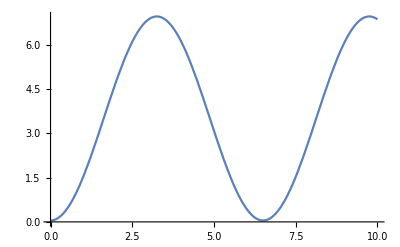

```mathematica
(*Antideriavtive is smooth*)
Plot[int /.values /. ζ-> 0.1 /. η->0.4 , {z, 0, 10}]
```

```mathematica
PowerExpand[Series[2Sqrt[exp4] , {z, 0, 4}]] //Simplify
```

(√(20+2 √10 χm) √(10 m-χm^2+χm^2 m') z)/(√m √(√10+χm) √(10 m-χm^2+10 m'))-(ⅈ (10 √10+20 χm+√10 χm^2) √(10 m-χm^2+χm^2 m') (-400 m^2+10 m (50+χm^2)+χm^2 (-50+3 χm^2)-10 (10+40 m-3 χm^2) m') z^3)/(120 √2 √m (√10+χm)^(3/2) √(10+√10 χm) (-10 m+χm^2-10 m')^(3/2))+O[z]^5

```mathematica
a0=-((α^2+χm^2)/(2 m (1+α^2)))^-1/.α-> (√(m+χm^2))/(√(1-m)) //Simplify
```

-2

```mathematica
(-6+a[0,0]^2-2 m a[0,0]^2+3 χm^2 a[0,0]^2)/(12 a[0,0]^3) /. a[0,0] -> -2 //Simplify
```

1/48 (1+4 m-6 χm^2)

```mathematica
Simplify[(-α^2-4 m α^2+5 α^4-4 m α^4-χm^2-4 m χm^2+8 α^2 χm^2-4 m α^2 χm^2-3 α^4 χm^2+3 χm^4-3 α^2 χm^4)/(24 m (1+α^2)^2)/.α-> (√(m+χm^2))/(√(1-m))]
```

1/24 (-1+2 m-3 χm^2)

```mathematica
v[y]-1/4 u[0,y]^2 (Derivative[0,1][u][0,y])^2 /. v[y]->JacobiSN[y,m]^2/JacobiDN[y,m]^2(1- χm^2 JacobiSN[y,m]^2) /. u[0,y]-> 2Sqrt[exp4/. z->y] /. D[u[0,y]-> 2Sqrt[exp4/.z->y], y] //FullSimplify
```

(JacobiSN[y,m]^2 (1-χm^2 JacobiSN[y,m]^2+(JacobiDN[y,m]^4 (-10+χm^2 JacobiSN[y,m]^2) (10 m-χm^2+χm^2 m')^2)/((m (-10 m+χm^2) JacobiCN[y,m]^2+m (-10+χm^2 JacobiSN[y,m]^2) m')^2)))/JacobiDN[y,m]^2

```mathematica
Normal@Series[v[y]-1/4 u[0,y]^2 (Derivative[0,1][u][0,y])^2 /. v[y]->JacobiSN[y,m]^2/JacobiDN[y,m]^2(1- χm^2 JacobiSN[y,m]^2) /. u[0,y]-> 2Sqrt[exp4/. z->y] /. D[u[0,y]-> 2Sqrt[exp4/.z->y], y],{y,0,6}]
```

y^4 (1/3 (-1+2 m-3 χm^2)+((10+√10 χm) (10 m-χm^2+χm^2 m')^2 (5000 √10 m-4000 √10 m^2+10000 m χm-8000 m^2 χm-500 √10 χm^2+600 √10 m χm^2-400 √10 m^2 χm^2-1000 χm^3+200 m χm^3-20 √10 χm^4+10 √10 m χm^4+60 χm^5+3 √10 χm^6-1000 √10 m'-4000 √10 m m'-2000 χm m'-8000 m χm m'+200 √10 χm^2 m'-400 √10 m χm^2 m'+600 χm^3 m'+30 √10 χm^4 m'))/(30 m^2 (√10+χm)^3 (-10 m+χm^2-10 m')^3))+y^2 (1-(((χm^2 (10+√10 χm))/(10 (√10+χm))-((10 m-χm^2) (-10+χm^2))/(√10 (10 m-χm^2+10 m')))^2)/m^2)+y^6 (1/45 (2-17 m+17 m^2+30 χm^2-15 m χm^2)+1/m^2(-((χm^2 (-100 √10-400 √10 m-200 χm-800 m χm+20 √10 χm^2-40 √10 m χm^2+60 χm^3+3 √10 χm^4))/(600 (√10+χm)^2)+(√(10 m-χm^2) ((√(10 m-χm^2) (-100 √10-400 √10 m+100 √10 χm^2+40 √10 m χm^2-9 √10 χm^4))/(6000 (1+(10 m-χm^2)/(10 m')) √m')+((10 m-χm^2)^(3/2) (-10+χm^2)^2 √m')/(10 √10 (10 m-χm^2+10 m')^2)))/(√m'))^2-2 ((χm^2 (10+√10 χm))/(10 (√10+χm))-((10 m-χm^2) (-10+χm^2))/(√10 (10 m-χm^2+10 m'))) (1/(24000 (√10+χm)^3)χm^2 (2000+88000 m+32000 m^2+600 √10 χm+26400 √10 m χm+9600 √10 m^2 χm-5400 χm^2+14400 m χm^2+9600 m^2 χm^2-1780 √10 χm^3-2720 √10 m χm^3+320 √10 m^2 χm^3-900 χm^4-3600 m χm^4+210 √10 χm^5-120 √10 m χm^5+270 χm^6+9 √10 χm^7)+1/(√m')√(10 m-χm^2) (-(√(10 m-χm^2) (-40-1760 m-640 m^2+364 χm^2+896 m χm^2+64 m^2 χm^2-126 χm^4-72 m χm^4+9 χm^6))/(4800 √10 (1+(10 m-χm^2)/(10 m')) √m')-(√(10 m-χm^2) (-10+χm^2) (((10 m-χm^2)^2 (-10+χm^2)^2)/(10000 (1+(10 m-χm^2)/(10 m'))^2 (m')^2)-((10 m-χm^2) (1/10 (1/4+1/12 (1+4 m))-χm^2/100+1/10 (-χm^2/30-(m χm^2)/30+χm^4/100)))/((1+(10 m-χm^2)/(10 m')) m')))/(10 √10 (1+(10 m-χm^2)/(10 m')) √m')-((10 m-χm^2)^(3/2) (-10+χm^2) (-100 √10-400 √10 m+100 √10 χm^2+40 √10 m χm^2-9 √10 χm^4) √m')/(6000 (10 m-χm^2+10 m')^2)))))

```mathematica
Normal@Series[v[y]-1/4 u[0,y]^2 (Derivative[0,1][u][0,y])^2 /. v[y]->Normal@Series[JacobiSN[y,m]^2/JacobiDN[y,m]^2(1- χm^2 JacobiSN[y,m]^2),{y,0,8}] /. u[0,y]-> PowerExpand@Normal@Series[2Sqrt[exp4/. z->y],{y,0,8}] /. D[u[0,y]-> PowerExpand@Normal@Series[2Sqrt[exp4/.z->y],{y,0,8}], y] //PowerExpand,{y,0,10}]
```

1/5529600 y^10 (-779+76568 m-441032 m^2+728928 m^3-364464 m^4-150020 χm^2+734680 m χm^2-764080 m^2 χm^2+496160 m^3 χm^2-509650 χm^4-1134200 m χm^4-219400 m^2 χm^4+1095900 χm^6+721800 m χm^6-634875 χm^8)

```mathematica
PowerExpand@Normal@Series[2Sqrt[exp4/.z->y],{y,0,8}]
```

√2 y+(y^3 (-1+2 m-3 χm^2))/(12 √2)+(y^5 (1-36 m+36 m^2+70 χm^2+20 m χm^2-55 χm^4))/(960 √2)+(y^7 (-1+838 m-2508 m^2+1672 m^3-1673 χm^2-3612 m χm^2-868 m^2 χm^2+5285 χm^4+2870 m χm^4-3675 χm^6))/(161280 √2)

```mathematica
TeXForm[(α ArcTan[α]-α ArcTan[(α JacobiCN[z,m])/(√(1+χm^2 JacobiSN[z,m]^2))]+ⅈ χm (Log[1+ⅈ χm]-Log[ⅈ χm JacobiCN[z,m]+√(1+χm^2 JacobiSN[z,m]^2)]))/m]
```

\frac{\alpha  \tan ^{-1}(\alpha )-\alpha  \tan ^{-1}\left(\frac{\alpha  \text{cn}(z|m)}{\sqrt{\text{$\chi $m}^2
   \text{sn}(z|m)^2+1}}\right)+i \text{$\chi $m} \left(\log (1+i \text{$\chi $m})-\log \left(\sqrt{\text{$\chi $m}^2
   \text{sn}(z|m)^2+1}+i \text{$\chi $m} \text{cn}(z|m)\right)\right)}{m}